## Program

```mathematica
recBox[{x1_,y1_},{x2_,y2_}]:=Line[{{x1,y1},{x2,y1},{x2,y2},{x1,y2},{x1,y1}}]
```

```mathematica
recBox[{x1_,y1_},{x2_,y2_},tx_]:={Line[{{x1,y1},{x2,y1},{x2,y2},{x1,y2},{x1,y1}}],Text[tx,{(x1+x2)/2,(y1+y2)/2}]}
```

```mathematica
recBox[{x1_,y1_},{x2_,y2_},{tx_,s_}]:={Line[{{x1,y1},{x2,y1},{x2,y2},{x1,y2},{x1,y1}}],Text[Style[tx,FontSize->s],{(x1+x2)/2,(y1+y2)/2}]}
```

```mathematica
circleText[cood_,r_,tx_]:={Circle[cood,r],Text[tx,cood]}
```

```mathematica
circleText[cood_,r_,{tx_,s_}]:={Circle[cood,r],Text[Style[tx,FontSize->s],cood]}
```

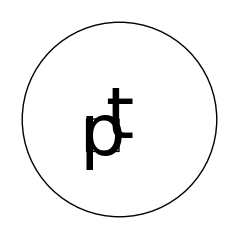

```mathematica
Graphics[{recBox[{0,0},{1,1},{"p",120}],circleText[{1,1},3,{"t",100}]}]
```

```mathematica
cons[{Null},cood_]:={recBox[cood,cood+1],recBox[cood+{1,0},cood+{2,1}],Line[{cood+{1,0},cood+{2,1}}]}
```

```mathematica
cons[{x_},cood_]:={recBox[cood,cood+1],recBox[cood+{1,0},cood+{2,1}],Line[{cood+{1,0},cood+{2,1}}],Line[{cood+0.5,cood+0.5+{0,-1}}],circleText[cood+0.5+{0,-1.5},0.5,{x,16}]}
```

```mathematica
cons[{x_,y__},cood_]:={recBox[cood,cood+1],recBox[cood+{1,0},cood+{2,1}],Line[{cood+{1.5,0.5},cood+{1.5,0.5}+{1,0}}],Line[{cood+0.5,cood+0.5+{0,-1}}],circleText[cood+0.5+{0,-1.5},0.5,{x,16}],cons[{y},cood+{2.5,0}]}
```

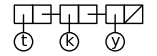

```mathematica
Graphics[cons[{t,k,y},{1,1}]]
```

## Figure

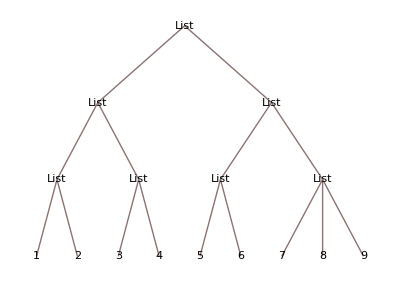

```mathematica
TreeForm[{{{1,2},{3,4}},{{5,6},{7,8,9}}}]
```

#### Fig[zu-cell]

```mathematica
li={1,2,{3,4}}
```

{1,2,{3,4}}

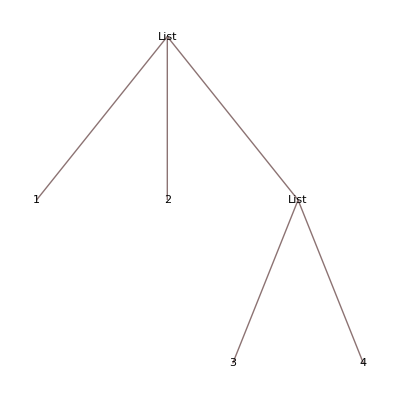

```mathematica
TreeForm[li]
```

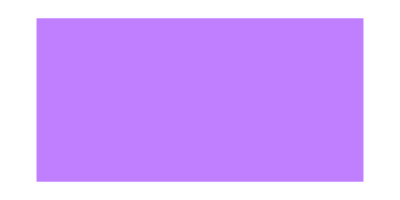

```mathematica
Graphics[{RGBColor[0.5,0,5,0.5],Rectangle[{1,1},{3,2}],Text[""]}]
```